```mathematica
{1,2,4,11}
```

{1,2,4,11}

```mathematica
FindSequenceFunction[{1,2,4,11}]
```

FindSequenceFunction[{1,2,4,11}]

```mathematica
Accumulate[{1,2,4,11}]
```

{1,3,7,18}

```mathematica
FindSequenceFunction[Accumulate[{1,2,4,11}]]
```

FindSequenceFunction[{1,3,7,18}]

```mathematica
Join[{{{1}}},{{{2}}}]
```

{{{1}},{{2}}}

```mathematica
Join[{{{1}}},{{{{2}}}}]
```

{{{1}},{{{2}}}}

```mathematica
{1,2}
```

```mathematica
{1,2}
```

```mathematica
{{1,2},{}}
```

```mathematica
{{1},{2}}
```

{{1},{2}}

```mathematica
Join[{{1}},{{2}},2]
```

{{1,2}}

```mathematica
Join[Join[{{1}},{{2}},2],{{}},1]
```

{{1,2},{}}

```mathematica
Join[Join[{{1}},{{}},2],{{2}},1]
```

{{1},{2}}

```mathematica
SamePile//ClearAll
SamePile[currentpile_,newelement_]:=Join[Join[currentpile,{{newelement}},2],{{}},1]
```

```mathematica
NewPile//ClearAll
NewPile[currentpile_,newelement_]:=Join[Join[currentpile,{{}},2],{{newelement}},1]
```

```mathematica
SamePile[{{1}},2]
```

{{1,2},{}}

```mathematica
NewPile[{{1}},2]
```

{{1},{2}}

```mathematica
SamePile[SamePile[{{1}},2],3]
```

{{1,2,3},{},{}}

```mathematica
SamePile[SamePile[SamePile[{{1}},2],3],4]
```

{{1,2,3,4},{},{},{}}

```mathematica
NewPile[SamePile[SamePile[SamePile[{{1}},2],3],4],5]
```

{{1,2,3,4},{},{},{},{5}}

```mathematica
Join[{{1,2},{}},{{3}},2]
```

{{1,2,3},{}}

```mathematica
Join[{{1,2},{}},{{3}},2]
```

{{1,2,3},{}}

```mathematica
Join[Join[{{1,2},{}},{{3}},2],{{}},1]
```

{{1,2,3},{},{}}

## using the functions

```mathematica
startPile={{1}}
```

{{1}}

```mathematica
SamePile[{{1}},2]
```

{{1,2},{}}

```mathematica
NewPile[{{1}},2]
```

{{1},{2}}

```mathematica
SamePile[SamePile[{{1}},2],3]
```

{{1,2,3},{},{}}

```mathematica
NewPile[SamePile[{{1}},2],3]
```

{{1,2},{},{3}}

```mathematica
SamePile[NewPile[{{1}},2],3]
```

{{1,3},{2},{}}

```mathematica
NewPile[NewPile[{{1}},2],3]
```

{{1},{2},{3}}

## 4 cards

```mathematica
SamePile[SamePile[SamePile[{{1}},2],3],4]
```

{{1,2,3,4},{},{},{}}

```mathematica
SamePile[NewPile[SamePile[{{1}},2],3],4]
```

{{1,2,4},{},{3},{}}

```mathematica
SamePile[SamePile[NewPile[{{1}},2],3],4]
```

{{1,3,4},{2},{},{}}

```mathematica
SamePile[NewPile[NewPile[{{1}},2],3],4]
```

{{1,4},{2},{3},{}}

```mathematica
NewPile[SamePile[SamePile[{{1}},2],3],4]
```

{{1,2,3},{},{},{4}}

```mathematica
NewPile[NewPile[SamePile[{{1}},2],3],4]
```

{{1,2},{},{3},{4}}

```mathematica
NewPile[SamePile[NewPile[{{1}},2],3],4]
```

{{1,3},{2},{},{4}}

```mathematica
NewPile[NewPile[NewPile[{{1}},2],3],4]
```

{{1},{2},{3},{4}}

## Removing piles of 4

```mathematica
PileHasFourCardsRemoved//ClearAll
PileHasFourCardsRemoved[piles_]:=Select[Length[#]!=4&][piles]
```

```mathematica
PileHasFourCardsRemoved[{{1,2,3,4},{},{},{}}]
```

{{},{},{}}

```mathematica
SamePile[PileHasFourCardsRemoved[{{1,2,3,4},{},{},{}}],5]
```

{{5},{},{},{}}

```mathematica
NewPile[PileHasFourCardsRemoved[{{1,2,3,4},{},{},{}}],5]
```

{{},{},{},{5}}

```mathematica
FoldPairList[{p[#1,#2],q[#1,#2]}&,u,{1,2,3},g]
```

{g[{p[u,1],q[u,1]}],g[{p[q[u,1],2],q[q[u,1],2]}],g[{p[q[q[u,1],2],3],q[q[q[u,1],2],3]}]}

```mathematica
FoldPairList[{p[#1,#2],q[#1,#2]}&,u,{b,c,d},g]
```

{g[{p[u,b],q[u,b]}],g[{p[q[u,b],c],q[q[u,b],c]}],g[{p[q[q[u,b],c],d],q[q[q[u,b],c],d]}]}

```mathematica
FoldPairList[{p[#1,#2],q[#1,#2]}&,{{1}},{b,c,d},g]
```

{g[{p[{{1}},b],q[{{1}},b]}],g[{p[q[{{1}},b],c],q[q[{{1}},b],c]}],g[{p[q[q[{{1}},b],c],d],q[q[q[{{1}},b],c],d]}]}

```mathematica
FoldPairList[{SamePile[#1,#2],NewPile[#1,#2]}&,{{1}},{2,3,4},g]
```

{g[{{{1,2},{}},{{1},{2}}}],g[{{{1,3},{2},{}},{{1},{2},{3}}}],g[{{{1,4},{2},{3},{}},{{1},{2},{3},{4}}}]}

```mathematica
{{{1,2},{}},3}
```

{{{1,2},{}},3}

```mathematica
NewPile@@{{{1,2},{}},3}
```

{{1,2},{},{3}}

```mathematica
SamePile@@{{{1,2},{}},3}
```

{{1,2,3},{},{}}

```mathematica
SequenceFoldList[f,{x,y},{a,b,c}]
```

{x,y,f[x,y,a],f[y,f[x,y,a],b],f[f[x,y,a],f[y,f[x,y,a],b],c]}

```mathematica
SequenceFoldList[f,{{{1}}},{a,b,c}]
```

{{{1}},f[{{1}},a],f[f[{{1}},a],b],f[f[f[{{1}},a],b],c]}

```mathematica
SequenceFoldList[f,{{{1}}},{2,b,c}]
```

{{{1}},f[{{1}},2],f[f[{{1}},2],b],f[f[f[{{1}},2],b],c]}

```mathematica
SequenceFoldList[NewPile,{{{1}}},{2,3,4}]
```

{{{1}},{{1},{2}},{{1},{2},{3}},{{1},{2},{3},{4}}}

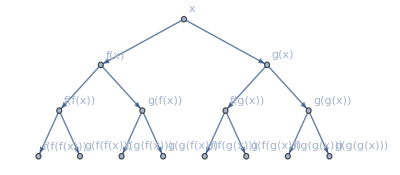

```mathematica
NestGraph[{f[#],g[#]}&,x,3,VertexLabels->Automatic]
```

```mathematica
PilePossibilities//ClearAll
```

```mathematica
{{1},{2,3},{4,5,6}}
```

{{1},{2,3},{4,5,6}}

```mathematica
Flatten[{{1},{2,3},{4,5,6}}]
```

{1,2,3,4,5,6}

```mathematica
Max[Flatten[{{1},{2,3},{4,5,6}}]]
```

6

```mathematica
Join[#,{7}]&/@{{1},{2,3},{4,5,6}}
```

{{1,7},{2,3,7},{4,5,6,7}}

```mathematica
Join[#,{7},{2}]&/@{{1},{2,3},{4,5,6}}
```

{{1,7,2},{2,3,7,2},{4,5,6,7,2}}

```mathematica
MapAt[Join[#,{7}]&,{{1},{2,3},{4,5,6}},1]
```

{{1,7},{2,3},{4,5,6}}

```mathematica
MapAt[Join[#,{7}]&,{{1},{2,3},{4,5,6}},2]
```

{{1},{2,3,7},{4,5,6}}

```mathematica
MapAt[Join[#,{7}]&,{{1},{2,3},{4,5,6}},3]
```

{{1},{2,3},{4,5,6,7}}

```mathematica
Length[{{1},{2,3},{4,5,6}}]
```

3

```mathematica
MapAt[Join[#,{}]&,{{1},{2,3},{4,5,6}},#]&/@Range[Length[{{1},{2,3},{4,5,6}}]]
```

{{{1,7},{2,3},{4,5,6}},{{1},{2,3,7},{4,5,6}},{{1},{2,3},{4,5,6,7}}}

```mathematica
PilePossibilities//ClearAll
PilePossibilities[l_]:=Block[{newElement},newElement=Max[Flatten[l]]+1;Join[DeleteCases[MapAt[Join[#,{newElement}]&,l,#],x_/;Length[x]==4]&/@Range[Length[l]],{Join[l,{{newElement}}]}]]
```

```mathematica
PilePossibilities[{{1},{2,3},{4,5,6}}]
```

{{{1,7},{2,3},{4,5,6}},{{1},{2,3,7},{4,5,6}},{{1},{2,3}},{{1},{2,3},{4,5,6},{7}}}

```mathematica
{{1},{2,3},{4,5,6,7}}
```

{{1},{2,3},{4,5,6,7}}

```mathematica
Select[Length[#]==4&][{{1},{2,3},{4,5,6,7}}]
```

{{4,5,6,7}}

```mathematica
DeleteCases[{{1},{2,3},{4,5,6,7}},x_/;Length[x]==4]
```

{{1},{2,3}}

```mathematica
{{1},{2,3},{4,5,6,7}}
```

{{1},{2,3},{4,5,6,7}}

```mathematica
Max[Flatten[{{1},{2,3},{4,5,6,7}}]]+1
```

8

```mathematica
Join[{{1},{2,3},{4,5,6,7}},{{Max[Flatten[{{1},{2,3},{4,5,6,7}}]]+1}}]
```

{{1},{2,3},{4,5,6,7},{8}}

```mathematica
Join[{{1},{2,3},{4,5,6}},{{Max[Flatten[{{1},{2,3},{4,5,6}}]]+1}}]
```

{{1},{2,3},{4,5,6},{7}}

```mathematica
PilePossibilities[{{1}}]
```

{{{1,2}},{{1},{2}}}

```mathematica
PilePossibilities/@PilePossibilities[{{1}}]
```

{{{{1,2,3}},{{1,2},{3}}},{{{1,3},{2}},{{1},{2,3}},{{1},{2},{3}}}}

```mathematica
PilePossibilities/@PilePossibilities/@PilePossibilities[{{1}}]
```

{{{{{1,2,3},4},{{1,2},{3}}},{{{1,2,3}},{{1,2},{3},4}},{{{1,2,3}},{{1,2},{3}},{4}}},{{{{1,3},{2},4},{{1},{2,3}},{{1},{2},{3}}},{{{1,3},{2}},{{1},{2,3},4},{{1},{2},{3}}},{{{1,3},{2}},{{1},{2,3}}},{{{1,3},{2}},{{1},{2,3}},{{1},{2},{3}},{4}}}}

```mathematica
Flatten[PilePossibilities/@PilePossibilities/@PilePossibilities[{{1}}],2]
```

{{{1,2,3},4},{{1,2},{3}},{{1,2,3}},{{1,2},{3},4},{{1,2,3}},{{1,2},{3}},{4},{{1,3},{2},4},{{1},{2,3}},{{1},{2},{3}},{{1,3},{2}},{{1},{2,3},4},{{1},{2},{3}},{{1,3},{2}},{{1},{2,3}},{{1,3},{2}},{{1},{2,3}},{{1},{2},{3}},{4}}

```mathematica
Length[Flatten[PilePossibilities/@PilePossibilities/@PilePossibilities[{{1}}],2]]
```

19

```mathematica
1+2+4+12
```

19

```mathematica
Dimensions[{{1,2,3},4}]
```

{2}

```mathematica
ArrayReshape[]
```

```mathematica
PilePossibilities/@{{1}}
```

{{{Join[1,{2}]},{1,{2}}}}

```mathematica
PilePossibilities/@{{{1}}}
```

{{{{1,2}},{{1},{2}}}}

```mathematica
PilePossibilities/@PilePossibilities/@{{{1}}}
```

{{{{{1,2},3},{{1},{2}}},{{{1,2}},{{1},{2},3}},{{{1,2}},{{1},{2}},{3}}}}

```mathematica
Nest[PilePossibilities/@#&,{{{1}}},1]
```

{{{{1,2}},{{1},{2}}}}

```mathematica
Nest[PilePossibilities/@#&,{{{1}}},2]
```

{{{{{1,2},3},{{1},{2}}},{{{1,2}},{{1},{2},3}},{{{1,2}},{{1},{2}},{3}}}}

```mathematica
Nest[PilePossibilities/@#&,{{{1}}},3]
```

{{{{{{1,2},3},{{1},{2}},4},{{{1,2}},{{1},{2},3}},{{{1,2}},{{1},{2}},{3}}},{{{{1,2},3},{{1},{2}}},{{{1,2}},{{1},{2},3},4},{{{1,2}},{{1},{2}},{3}}},{{{{1,2},3},{{1},{2}}},{{{1,2}},{{1},{2},3}}},{{{{1,2},3},{{1},{2}}},{{{1,2}},{{1},{2},3}},{{{1,2}},{{1},{2}},{3}},{4}}}}

```mathematica
Nest[PilePossibilities/@#&,{{{1}}},7]
```

```mathematica
Flatten[Nest[PilePossibilities/@#&,{{{1}}},3],2]
```

{{{{1,2},3},{{1},{2}},4},{{{1,2}},{{1},{2},3}},{{{1,2}},{{1},{2}},{3}},{{{1,2},3},{{1},{2}}},{{{1,2}},{{1},{2},3},4},{{{1,2}},{{1},{2}},{3}},{{{1,2},3},{{1},{2}}},{{{1,2}},{{1},{2},3}},{{{1,2},3},{{1},{2}}},{{{1,2}},{{1},{2},3}},{{{1,2}},{{1},{2}},{3}},{4}}

```mathematica
Dimensions[Nest[PilePossibilities/@#&,{{{1}}},4],3]
```

{1,5}

```mathematica
Dimensions@ArrayFlatten[Nest[PilePossibilities/@#&,{{{1}}},4]]
```

{3,7}

```mathematica
Map[Length,ArrayFlatten[Nest[PilePossibilities/@#&,{{{1}}},4]],{3}]
```

{{{3,2},{3,2},{2,2,0},{1,3},{1,2,1},{3,3,2,5},{3,3,2,4,1}},{{3,2},{3,2},{2,2},{1,3,0},{1,2,1},{3,3,2,5},{3,3,2,4,1}},{{3,2},{3,2},{2,2},{1,3},5,{3,3,2,5},{3,3,2,4,1}}}

```mathematica
Flatten[Map[Length,ArrayFlatten[Nest[PilePossibilities/@#&,{{{1}}},4]],{3}]]
```

{3,2,3,2,2,2,0,1,3,1,2,1,3,3,2,5,3,3,2,4,1,3,2,3,2,2,2,1,3,0,1,2,1,3,3,2,5,3,3,2,4,1,3,2,3,2,2,2,1,3,5,3,3,2,5,3,3,2,4,1}

```mathematica
Total[Flatten[Map[Length,ArrayFlatten[Nest[PilePossibilities/@#&,{{{1}}},4]],{3}]]]
```

145

```mathematica
Total[Flatten[Map[Length,ArrayFlatten[Nest[PilePossibilities/@#&,{{{1}}},2]],{3}]]]
```

19

```mathematica
Total[Flatten[Map[Length,ArrayFlatten[Nest[PilePossibilities/@#&,{{{1}}},3]],{3}]]]
```

56

```mathematica
1+2+4+12+41
```

60

```mathematica
PilePossibilities[{{1}}]
```

{{{1,2}},{{1},{2}}}

```mathematica
PilePossibilities/@PilePossibilities[{{1}}]
```

{{{{1,2,3}},{{1,2},{3}}},{{{1,3},{2}},{{1},{2,3}},{{1},{2},{3}}}}

```mathematica
PilePossibilities/@PilePossibilities/@PilePossibilities[{{1}}]
```

{{{{{1,2,3},4},{{1,2},{3}}},{{{1,2,3}},{{1,2},{3},4}},{{{1,2,3}},{{1,2},{3}},{4}}},{{{{1,3},{2},4},{{1},{2,3}},{{1},{2},{3}}},{{{1,3},{2}},{{1},{2,3},4},{{1},{2},{3}}},{{{1,3},{2}},{{1},{2,3}}},{{{1,3},{2}},{{1},{2,3}},{{1},{2},{3}},{4}}}}

```mathematica
PilePossibilities/@PilePossibilities/@PilePossibilities/@PilePossibilities[{{1}}]
```

{{{{{{1,2,3},4},{{1,2},{3}},5},{{{1,2,3}},{{1,2},{3},4}},{{{1,2,3}},{{1,2},{3}},{4}}},{{{{1,2,3},4},{{1,2},{3}}},{{{1,2,3}},{{1,2},{3},4},5},{{{1,2,3}},{{1,2},{3}},{4}}},{{{{1,2,3},4},{{1,2},{3}}},{{{1,2,3}},{{1,2},{3},4}}},{{{{1,2,3},4},{{1,2},{3}}},{{{1,2,3}},{{1,2},{3},4}},{{{1,2,3}},{{1,2},{3}},{4}},{5}}},{{{{{1,3},{2}},{{1},{2,3},4},{{1},{2},{3}}},{{{1,3},{2}},{{1},{2,3}}}},{{{{1,3},{2},4},{{1},{2,3}},{{1},{2},{3}}},{{{1,3},{2}},{{1},{2,3}}}},{{{{1,3},{2},4},{{1},{2,3}},{{1},{2},{3}}},{{{1,3},{2}},{{1},{2,3},4},{{1},{2},{3}}},{{{1,3},{2}},{{1},{2,3}},5}},{{{{1,3},{2},4},{{1},{2,3}},{{1},{2},{3}}},{{{1,3},{2}},{{1},{2,3},4},{{1},{2},{3}}},{{{1,3},{2}},{{1},{2,3}}},{{{1,3},{2}},{{1},{2,3}},{{1},{2},{3}},{4},5}},{{{{1,3},{2},4},{{1},{2,3}},{{1},{2},{3}}},{{{1,3},{2}},{{1},{2,3},4},{{1},{2},{3}}},{{{1,3},{2}},{{1},{2,3}}},{{{1,3},{2}},{{1},{2,3}},{{1},{2},{3}},{4}},{5}}}}

```mathematica
First[PilePossibilities/@PilePossibilities/@PilePossibilities/@PilePossibilities[{{1}}]]
```

{{{{{1,2,3},4},{{1,2},{3}},5},{{{1,2,3}},{{1,2},{3},4}},{{{1,2,3}},{{1,2},{3}},{4}}},{{{{1,2,3},4},{{1,2},{3}}},{{{1,2,3}},{{1,2},{3},4},5},{{{1,2,3}},{{1,2},{3}},{4}}},{{{{1,2,3},4},{{1,2},{3}}},{{{1,2,3}},{{1,2},{3},4}}},{{{{1,2,3},4},{{1,2},{3}}},{{{1,2,3}},{{1,2},{3},4}},{{{1,2,3}},{{1,2},{3}},{4}},{5}}}

```mathematica
Part[PilePossibilities/@PilePossibilities/@PilePossibilities/@PilePossibilities[{{1}}],2]
```

{{{{{1,3},{2}},{{1},{2,3},4},{{1},{2},{3}}},{{{1,3},{2}},{{1},{2,3}}}},{{{{1,3},{2},4},{{1},{2,3}},{{1},{2},{3}}},{{{1,3},{2}},{{1},{2,3}}}},{{{{1,3},{2},4},{{1},{2,3}},{{1},{2},{3}}},{{{1,3},{2}},{{1},{2,3},4},{{1},{2},{3}}},{{{1,3},{2}},{{1},{2,3}},5}},{{{{1,3},{2},4},{{1},{2,3}},{{1},{2},{3}}},{{{1,3},{2}},{{1},{2,3},4},{{1},{2},{3}}},{{{1,3},{2}},{{1},{2,3}}},{{{1,3},{2}},{{1},{2,3}},{{1},{2},{3}},{4},5}},{{{{1,3},{2},4},{{1},{2,3}},{{1},{2},{3}}},{{{1,3},{2}},{{1},{2,3},4},{{1},{2},{3}}},{{{1,3},{2}},{{1},{2,3}}},{{{1,3},{2}},{{1},{2,3}},{{1},{2},{3}},{4}},{5}}}

```mathematica
PilePossibilities[{{1}}]
```

{{{1,2}},{{1},{2}}}

```mathematica
?FoldPairList
```

```mathematica
PilePossibilities/@PilePossibilities[{{1}}]
```

{{{{1,2,3}},{{1,2},{3}}},{{{1,3},{2}},{{1},{2,3}},{{1},{2},{3}}}}

```mathematica
{PilePossibilities/@PilePossibilities[{{1}}],3}
```

{{{{{1,2,3}},{{1,2},{3}}},{{{1,3},{2}},{{1},{2,3}},{{1},{2},{3}}}},3}

```mathematica
PilePossibilities//ClearAll
PilePossibilities[l_]:=Block[{newElement},newElement=Max[Flatten[l]]+1;Join[DeleteCases[MapAt[Join[#,{newElement}]&,l,#],x_/;Length[x]==4]&/@Range[Length[l]],{Join[l,{{newElement}}]}]]
```

```mathematica
Join[DeleteCases[MapAt[Join[#,{newElement}]&,l,#],x_/;Length[x]==4]&/@Range[Length[l]],{Join[l,{{newElement}}]}]
```

```mathematica
Function[b,{b[[1]]+1,b[[2]]+2}][{π,ⅇ}]
```

{1+π,2+ⅇ}

```mathematica
Function[l,{Join[DeleteCases[MapAt[Join[#,{l[[2]]}]&,l[[1]],#],x_/;Length[x]==4]&/@Range[Length[l[[1]]]],{Join[l[[1]],{{l[[2]]}}]}],l[[2]]+1}][{PilePossibilities/@PilePossibilities[{{1}}],3}]
```

{{{{{{1,2,3}},{{1,2},{3}},3},{{{1,3},{2}},{{1},{2,3}},{{1},{2},{3}}}},{{{{1,2,3}},{{1,2},{3}}}},{{{{1,2,3}},{{1,2},{3}}},{{{1,3},{2}},{{1},{2,3}},{{1},{2},{3}}},{3}}},4}

```mathematica
Function[l,{Join[DeleteCases[MapAt[Join[#,{l[[2]]}]&,l[[1]],#],x_/;Length[x]==4]&/@Range[Length[l[[1]]]],{Join[l[[1]],{{l[[2]]}}]}],l[[2]]+1}][{PilePossibilities/@PilePossibilities[{{1}}],3}]
```

```mathematica
{PilePossibilities[{{1}}],2}
```

{{{{1,2}},{{1},{2}}},2}

```mathematica
Function[l,{Join[DeleteCases[MapAt[Join[#,{l[[2]]+1}]&,l[[1]],#],x_/;Length[x]==4]&/@Range[Length[l[[1]]]],{Join[l[[1]],{{l[[2]]+1}}]}],l[[2]]+1}][{PilePossibilities[{{1}}],2}]
```

{{{{{1,2},3},{{1},{2}}},{{{1,2}},{{1},{2},3}},{{{1,2}},{{1},{2}},{3}}},3}

```mathematica
Function[l,{Join[DeleteCases[MapAt[Join[#,{l[[2]]+1}]&,l[[1]],#],x_/;Length[x]==4]&/@Range[Length[l[[1]]]],{Join[l[[1]],{{l[[2]]+1}}]}],l[[2]]+1}][{{{1}},1}]
```

{{{{1,2}},{{1},{2}}},2}

```mathematica
{PilePossibilities/@PilePossibilities[{{1}}],3}
```

{{{{{1,2,3}},{{1,2},{3}}},{{{1,3},{2}},{{1},{2,3}},{{1},{2},{3}}}},3}

```mathematica
MapAt[Join[#,{7}]&,{{1},{2,3},{4,5,6}},1]
```

{{1,7},{2,3},{4,5,6}}

```mathematica
MapAt[Join[#,{7}]&,{{1},{2,3},{4,5,6}},2]
```

{{1},{2,3,7},{4,5,6}}

```mathematica
MapAt[Join[#,{7}]&,{{1},{2,3},{4,5,6}},3]
```

{{1},{2,3},{4,5,6,7}}

```mathematica
DeleteCases[x_/;Length[x]==4][MapAt[Join[#,{7}]&,{{1},{2,3},{4,5,6}},#]]&/@Range[Length[{{1},{2,3},{4,5,6}}]]
```

{{{1,7},{2,3},{4,5,6}},{{1},{2,3,7},{4,5,6}},{{1},{2,3}}}

```mathematica
Append[DeleteCases[x_/;Length[x]==4][MapAt[Join[#,{7}]&,{{1},{2,3},{4,5,6}},#]]&/@Range[Length[{{1},{2,3},{4,5,6}}]],Join[{{1},{2,3},{4,5,6}},{{7}}]]
```

{{{1,7},{2,3},{4,5,6}},{{1},{2,3,7},{4,5,6}},{{1},{2,3}},{{1},{2,3},{4,5,6},{7}}}

```mathematica
Join[{{1},{2,3},{4,5,6}},{{7}}]
```

{{1},{2,3},{4,5,6},{7}}

```mathematica
Join[{{1},{2,3},{4,5,6}},{{7}}]
```

{{1},{2,3},{4,5,6},{7}}

```mathematica
Function[t,Append[DeleteCases[x_/;Length[x]==4][MapAt[Join[#,{7}]&,t,#]]&/@Range[Length[t]],Join[{{1},{2,3},{4,5,6}},{{7}}]]
```

```mathematica
Function[{t,c},Append[DeleteCases[x_/;Length[x]==4][MapAt[Join[#,{c}]&,t,#]]&/@Range[Length[t]],Join[t,{{c}}]]][{{1},{2,3},{4,5,6}},7]
```

{{{1,7},{2,3},{4,5,6}},{{1},{2,3,7},{4,5,6}},{{1},{2,3}},{{1},{2,3},{4,5,6},{7}}}

```mathematica
Function[{t,c},Append[DeleteCases[x_/;Length[x]==4][MapAt[Join[#,{c}]&,t,#]]&/@Range[Length[t]],Join[t,{{c}}]]][{{1,6},{2},{3},{4},{5}},7]
```

{{{1,6,7},{2},{3},{4},{5}},{{1,6},{2,7},{3},{4},{5}},{{1,6},{2},{3,7},{4},{5}},{{1,6},{2},{3},{4,7},{5}},{{1,6},{2},{3},{4},{5,7}},{{1,6},{2},{3},{4},{5},{7}}}

```mathematica
Function[l,Function[t,Append[DeleteCases[x_/;Length[x]==4][MapAt[Join[#,{l[[2]]+1}]&,t,#]]&/@Range[Length[t]],Join[t,{{l[[2]]+1}}]]]/@l[[1]]][{PilePossibilities/@PilePossibilities[{{1}}],3}]
```

{{{{{1,2,3},4},{{1,2},{3}}},{{{1,2,3}},{{1,2},{3},4}},{{{1,2,3}},{{1,2},{3}},{4}}},{{{{1,3},{2},4},{{1},{2,3}},{{1},{2},{3}}},{{{1,3},{2}},{{1},{2,3},4},{{1},{2},{3}}},{{{1,3},{2}},{{1},{2,3}}},{{{1,3},{2}},{{1},{2,3}},{{1},{2},{3}},{4}}}}

```mathematica
{PilePossibilities/@PilePossibilities[{{1}}],3}
```

{{{{{1,2,3}},{{1,2},{3}}},{{{1,3},{2}},{{1},{2,3}},{{1},{2},{3}}}},3}

```mathematica
Flatten[(PilePossibilities/@PilePossibilities[{{1}}]),1]
```

{{{1,2,3}},{{1,2},{3}},{{1,3},{2}},{{1},{2,3}},{{1},{2},{3}}}

```mathematica
Map[PilePossibilities,Flatten[(PilePossibilities/@PilePossibilities[{{1}}]),1],{1}]
```

{{{},{{1,2,3},{4}}},{{{1,2,4},{3}},{{1,2},{3,4}},{{1,2},{3},{4}}},{{{1,3,4},{2}},{{1,3},{2,4}},{{1,3},{2},{4}}},{{{1,4},{2,3}},{{1},{2,3,4}},{{1},{2,3},{4}}},{{{1,4},{2},{3}},{{1},{2,4},{3}},{{1},{2},{3,4}},{{1},{2},{3},{4}}}}

```mathematica
{{{{1}}},1}
```

{{{{1}}},1}

```mathematica
NewPilePossibilities//ClearAll
NewPilePossibilities[l_,r_]:=MapAt[Join[]]
```